# Physics 230 -- Lab 6 (Integration)

## Branton J. Campbell, BYU Physics & Astronomy, Winter 2010 R. Steven Turley, BYU Physics and Astronomy, Fall 2011

This lab is designed to familiarize you with Mathematica's tools for symbolic and numerical integration in the context of moderately-challenging math and physics problems.

## Introduction (10 minutes)

Numerical integration is where Mathematica particularly shines and was the historical impetus behind its development.  As you’ll remember from your calculus classes, the process of differentiation is usually straightforward and fairly mechanical.  On the other hand, there are a variety of sophisticated techniques necessary to be able to find closed-form solutions to integration problems.  Indeed, most of the definite integrals encountered in actual physics situations don’t have closed-form solutions and need to be numerically.

Mathematica has tools for solving both symbolic integrals and numerical integrals.  In this lab we’ll first cover techniques for symbolic integration and then follow them with examples of techniques for numerical integration.  The bulk of your time will be spent on applications of integration to physics problems.

### Data Representation

#### Numerical Data

This lab is a good time to consider various ways data can be stored in a computer and in particular how numerical and symbolic data is represented in Mathematica.  There are four basic numerical data types in Mathematica: integers, rational numbers, real numbers, and complex numbers.  At its heart, a computer deals with data as a collection of binary digits (1 or 0).  This section deals with how these digits are arranged and interpreted to represent various kinds of numerical values.

Integers are the same thing in Mathematica as they are in mathematics and physics.  Integers can be represented exactly on a computer.  Positive integers are represented as their values in base 2.  You can see this representation using the IntegerDigits or BaseForm functions.

```mathematica
IntegerDigits[11,2,16]
BaseForm[2459,2]
```

{0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,1}

100110011011_2

Rational numbers are ratios of two integers.  They can also be represented exactly on a computer by separtely storing their numerator and denominator.  Mathematica prints rational numbers as ratios.  It will keep operations on rational numers in an exact format until you force it to convert it to another format.  Notice how the results of the following operations are expressed as rational numbers.

```mathematica
1/2
8/12
1/2-1/3
(8-6)/(2+11/2)
```

1/2

2/3

1/6

4/15

Real numbers cannot generally be stored as rational numbers.  This is because most of them are not terminating fractions in base 2.    (Exceptions would be things that are rational nubmers in base 2 such as 1/2, 3/4, 11/16 and so forth.)  They are stored as an approximate mantissa (the first part of the number when written in scientific notation) and then as a power of ten exponent.  The default mantissa precision on the computers in our labs is about 16 digits.  You can see what it is using $MachinePrecision.

```mathematica
$MachinePrecision
```

15.9546

Mathematica is capable of using an arbitrary number of digits in calculations, but is much faster if the default $MachinePrecision is used.  The N function converts a number of an exact representation to a Real number.  It can specify an arbitrarily large number of digits of precision.  In the example below, the first expression is exact, the second is accurate to machine precision, and the final one is accurate to 250 digits.

```mathematica
Pi
N[Pi]
N[Pi,250]
```

π

3.14159

3.141592653589793238462643383279502884197169399375105820974944592307816406286208998628034825342117067982148086513282306647093844609550582231725359408128481117450284102701938521105559644622948954930381964428810975665933446128475648233786783165271201909

Note that even though N[Pi] is accurate to machine precision, only six significant digits are display.  You can see the full sixteen digits in several ways.  My favorite is

```mathematica
N[Pi]//InputForm
```

3.141592653589793

Complex numbers are stored as a pair of numbers.  These numbers can be Real, Integers, or Rationals.   The functions Re and Im can separate out the real and imaginary parts.  Depending on the type of their constituent parts, complex numbers are either be stored exactly or approximately.

```mathematica
z=5+6I
Re[z]
IntegerQ/@{Re[z],z}
Element[Im[1/2+6I/7], Rationals]
```

5+6 ⅈ

5

{True,False}

True

#### Other kinds of data

Symbols, strings, and expressions can also be considered as another kind of data in Mathematica, as can expressions.  Since these are somewhat specialized, we’ll consider them in detail later.  For completeness, a string is text enclosed in double quotes.

```mathematica
myString = "This is a string."
```

This is a string.

A symbol is a sequence of characters without quotes of “white spaces.”

```mathematica
mySymbol
```

mySymbol

An expressions is a sequence of symbols and operations.

```mathematica
myExpression = a+19-Sqrt[47]
```

a-√47+19

#### Accuracy and Precision

Mathematica usually does a pretty good job of hiding the details of accuracy and precision of internally stored nubmers from you.  It will try to give you answers to machine precision when possible (or to an accuracy you specify).  Many numerical routines can be queried to find the accuracy of their result.

Sometimes you’ll want to be careful about watching the accuracy of answers in your own routine, however.  For instance, consider the following example of using a simple formula for the approximate derivative of the sin(1).  From the definition of the derivative, the following should give a pretty good answer if dx is chosen small enough.

```mathematica
approxD[dx_]:=Abs(Sin[1+dx]-Sin[1-dx])/(2*dx)
```

We’ll modify it a bit to return the absolute value of the difference between its calculation and the exact answer.

```mathematica
exact = Cos[1.0];
approxD[dx_]:=Abs[N[(Sin[1+dx]-Sin[1-dx])/(2*dx),4]-exact]
```

If we plot this function, we’ll note that the accuracy of the calculation improves as dx gets smaller up to a point at about 10^-5 and then starts getting worse again because of the approximate nature of the real representation of the Cosine.  From that point on, the accuracy continues to get worse as dx is made smaller and smaller.

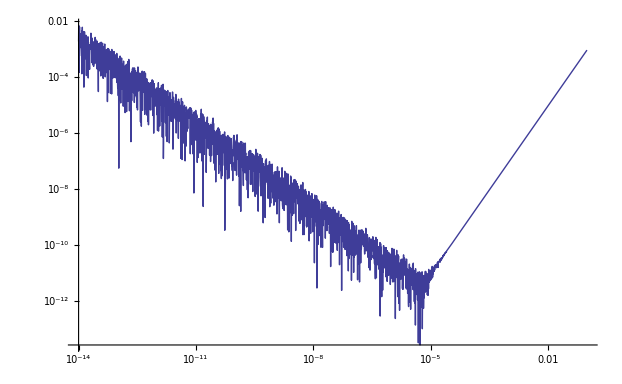

```mathematica
LogLogPlot[approxD[dx],{dx,10^-14,0.1}]
```

In calculations involving numerical dericatives (such as finite-difference solution techniques you’ll learn about in later courses), you need to be very aware of this issue.

### Operations with Numerical Data

When you apply functions to numerical data, Mathematica converts the results to the most simple and accurate form possible.  Thus, when possible, it expresses the result as an Integer.  If that isn’t possible it uses a Rational Result.  If that isn’t possible, it will use a Real result.  Complex results follow the same rules for their real and imaginary parts.  Consider the following examples.

```mathematica
1+3
1+4/5
7+2.5
3/27.0
```

4

9/5

9.5

0.111111

Mathematica will keep track of the precision of your intermediate results.  The answer will have an appropriate estimated precision, but as indicated below, it doesn’t always get it right.

```mathematica
Accuracy[1.0]
1.0-0.999999999999999
Accuracy[%]
```

15.9546

9.99201×10^-16

30.9549

## Symbolic Integration (30 min)

Begin by glancing through the Basic Examples and Scope and Options sections of the DC reference page for the Integrate function.  In the following exercises, you can refer to these examples as needed.

### (#1) Indefinite Integrals (10 min)

For each indefinite integral below, compute the integral and then plot it together the original (unintegrated) function on the same graph.  Use the PlotStyle option to give the two curves (or surfaces) different colors.  Hints: To save time, you are encouraged to use simple expressions (e.g. y=x^2) rather than argumentative functions (e.g. y[x_]:=x^2) for this exercise.

(a) ∫√(1+x^2)ⅆx   Plot both functions over the range {x, 0, 3}.

1/2 (√(x^2+1) x+sinh^-1(x))

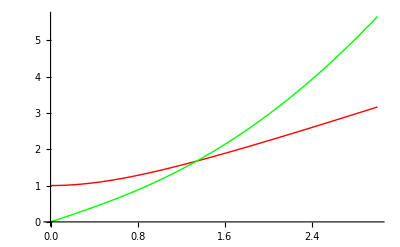

```mathematica
a1 = √(1+x^2);
a1i=Integrate[a1,x]
Plot[{a1,a1i},{x,0,3},PlotStyle->{Red,Green}]
```

(b) ∫sin(1/x)ⅆx   LogLinearPlot both functions over the range {x, 0.01, 10}.

x sin(1/x)-1/x

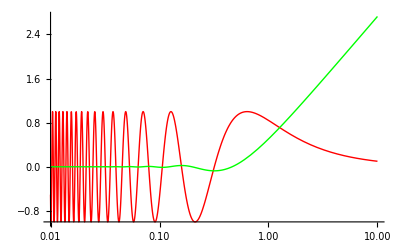

```mathematica
b1 = Sin[1/x];
b1i = Integrate[b1,x]
LogLinearPlot[{b1,b1i},{x,0.01,10},PlotStyle->{Red,Green}]
```

(c) ∫J_1(x)ⅆx   Plot both functions over the range {x, 0, 20}.  Note that J_1(x) is the first-order Bessel function (BesselJ) of the first kind.

1-0z

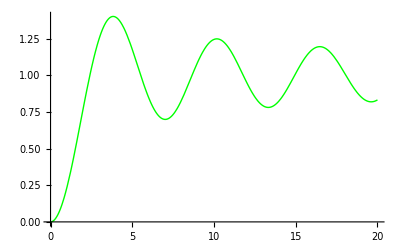

```mathematica
c1 = BesselJ[1,x];
c1i = Integrate[c1,{x,0,z}]
Plot[{c1,c1i},{z,0,20},PlotStyle->{Red,Green}]
```

(d) ∫ⅇ^(-x^2)ⅆx   Plot both functions over the range {x, -4, 4}.

1/2 √π erf(x)

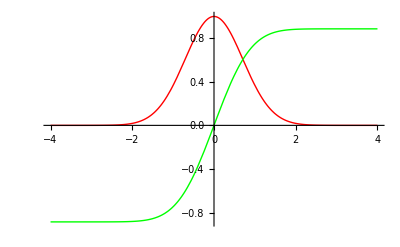

```mathematica
d1 = Exp[-x^2];
d1i = Integrate[d1,x]
Plot[{d1,d1i},{x,-4,4},PlotStyle->{Red,Green}]
```

### (#2) Multiple Integrals (10 min)

Compute the following indefinite integrals. To save time, you are encouraged to use simple expressions (e.g. f = x^2 + y^2) rather than argumentative functions (e.g. f[x_,y_] := x^2 + y^2) for this exercise.

(a) Compute ∫∫(x^2+y^2)ⅆxⅆy   Plot3D the function and it's indefinite integral on the same graph over the range {x, -2, 2} and  {y, -2, 2}.  Use the PlotStyle option to give the two curves (or surfaces) different colors.

```mathematica
a2 = x^2+y^2;
a2i = Integrate[a2,x,y]
Plot3D[{a2,a2i},{x,-2,2},{y,-2,2},PlotStyle->{Red,Green}]
```

1/3 x y (x^2+y^2)

-Graphics3D-

(b) Compute ∫∫sin(x y)ⅆxⅆy   Plot the function and it's indefinite integral on the same graph over the range {x, -π, π} and  {y, -π, π}.  Use the PlotStyle option to give the two curves (or surfaces) different colors.

```mathematica
b2 = Sin[x*y];
b2i = Integrate[b2,x,y]
Plot3D[{b2,b2i},{x,-π,π},{y,-π,π},PlotStyle->{Red,Green},PlotRange->All]
```

-x y

-Graphics3D-

(c) Compute ∫∫∫r^2 sin(θ)ⅆϕⅆθⅆr   Don't bother plotting this one.

```mathematica
c2 = r^2 Sin[θ];
c2i = Integrate[c3,ϕ,θ,r]
```

-1/3 r^3 ϕ cos(θ)

### (#3) Definite Integrals (5 min)

(a) Compute ∫_(-∞)^∞ (sin(x))/x ⅆx    Plot the integrand over the range {x, -8 π, 8 π} using the Filling → Axis and PlotRange → All options.

π

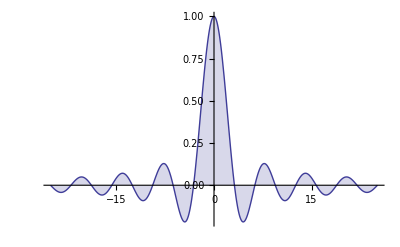

```mathematica
a3 = Sin[x]/x;
Integrate[a3,{x,-∞,∞}]
Plot[a3,{x,-8π,8π},PlotRange->All,Filling->Axis]
```

(b) Compute ∫_0^1 ln(x)ⅆx   Plot the integrand over the integration range using the Filling → Axis option.

-1

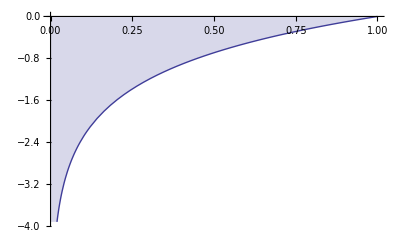

```mathematica
b3 =Log[x];
Integrate[b3,{x,0,1}]
Plot[b3,{x,0,1},Filling->Axis]
```

(c) Compute ∫_0^∞ x^2 ⅇ^-x ⅆx   Plot the integrand over the range {x, 0, 10} using the Filling → Axis option.

2

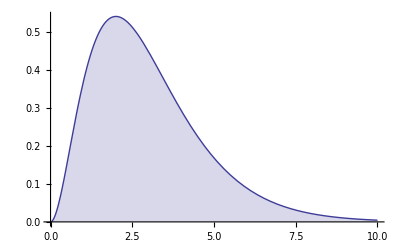

```mathematica
c3 = x^2 Exp[-x];
Integrate[c3,{x,0,∞}]
Plot[c3,{x,0,10},Filling->Axis]
```

### (#4) Integrate options (5 min)

(a)  Evaluate the cell below to visually verify that ∫_0^∞ ⅇ^(-s x)ⅆx converges as x → ∞ when s > 0, but diverges when s ≤ 0.  Each integral computes the area under its respective curve.

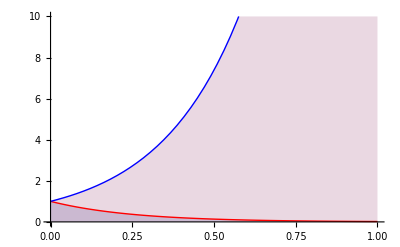

```mathematica
Plot[{Exp[-4 x],Exp[4x]},{x,0,1},Filling->Axis,PlotRange->{0,10},PlotStyle->{Red,Blue}]
```

(b) When we evaluate this integral with s as an unspecified variable parameter, Mathematica produces a logic statement than can be further evaluated after more information is provided about s.  In this case, Mathematica appears to consider the possibility that s might be either positive, negative or complex.

```mathematica
res = Integrate[Exp[-s x],{x,0,Infinity}]
```

ConditionalExpression[1/s,Re(s)>0]

(c) To provide additional information about the properties of s, we can either wrap the Assuming function around Integrate, or else employ the Assumptions option within Integrate.

```mathematica
Integrate[Exp[-s x],{x,0,Infinity},Assumptions-> {s<0}]
Assuming[s>0,  Integrate[Exp[-s x],{x,0,Infinity}]]
```

Integrate::idiv: Integral of TraditionalForm`ⅇ^-s\ x does not converge on TraditionalForm`{0, ∞}.

Integrate[ⅇ^(-s x),{x,0,∞},Assumptions→{s<0}]

1/s

(d) We can also inject a variety of assumptions after the integral has been computed.  Here are a few examples that involve Simplify, some of which are more useful than others.

```mathematica
res = Integrate[Exp[-s x],{x,0,Infinity}]
Simplify[res,s>0]
Simplify[res, s==0]
Simplify[res,s∈Reals]
Simplify[res, Re[s]==0]
```

ConditionalExpression[1/s,Re(s)>0]

1/s

Undefined

ConditionalExpression[1/s,s>0]

Undefined

(e) We can actually tell Mathematica to assume a simple choice for s that will lead to a simple result without having to specify any assumptions ourselves by using GenerateConditions → False, though this could lead to unexpected results.

```mathematica
Integrate[Exp[-s x],{x,0,Infinity},GenerateConditions->False]
```

1/s

(f) Sometimes, we might want to make global assumptions about a variable that will implicitly apply to all subsequent calculations.  Evaluate the cell below to see how this can be done.  Parameters like $Assumptions that have a "$" at the front are system variables that exist even if you don't define them.  Many system variables can be modied, as is the case here.

```mathematica
$Assumptions
```

True

```mathematica
$Assumptions = {s>0};
 Integrate[Exp[-s x],{x,0,Infinity}]
```

1/s

Some divergent integrals have a finite Cauchy principal value.  If interested, see the DC reference page on PrincipalValue for more information.  On a related topic, one can also calculate the Residue of a singular point in the complex plane.

## Numerical integration (30 min)

### (#5) Tutorial examples (15 min)

(a) Review the first two examples in each subsection  (excluding Monte Carlo integration) of the Scope section of the DC reference page on NIntegrate.

(b) Carefully read and work through the Numerical Mathematics tutorial, and explain to your TA how using NIntegrate is different than using a combination of N and Integrate.

(c) Carefully read and work through the tutorial on Numerical Precision, and explain to your TA how the WorkingPrecision and PrecisionGoal options affect the behavior of NIntegrate.  Note that computational "precision" refers to the number of significant digits in a result, while computational "accuracy" refers to the number of digits to the right of the decimal place?

(d) Quickly scan through the basic tutorial on Numerical Integration.  Look for examples that show you how to use MaxPoints and MaxRecursion to achieve greater control over the integration process.  Also look for examples where extra points have been inserted into the middle of the integration range to force the algorithm to watch out for peaks and/or singularities there.

### (#6) Advanced Options (15 min)

(a) Use Integrate to compute ∫_0^1 ∫_0^1 1/(√(x^2 + y^2))ⅆxⅆy exactly.  Then use N[%]//InputForm to obtain a numerical result and to see the digits of precision that are not displayed automatically.  Out to 15 significant digits (allowing for rounding in the last digit), the answer should be 1.76274717403909.

```mathematica
a6 = 1/(√(x^2+y^2));
Integrate[a6,{x,0,1},{y,0,1}]
N[Integrate[a6,{x,0,1},{y,0,1}]]//InputForm
```

2 sinh^-1(1)

1.762747174039086

(b) Use NIntegrate, together with Timing, to compute the integral above numerically, while also measuring the time spent on the integration.  The time spent should be right around 0.05 seconds.  Employ %[[2]]//InputForm to display all of the digits of precision available, and then compare your numerical result to the exact result above.

```mathematica
Abs[Timing[NIntegrate[a6,{x,0,1},{y,0,1}]]- Timing[Integrate[a6,{x,0,1},{y,0,1}]]]
NIntegrate[a6,{x,0,1},{y,0,1}]
```

{1.44844,2.18214×10^-8}

1.76275

(c) Now use NIntegrate to compute the numerical integral above to 15 digits of precision in less than 0.05 seconds.  Use PrecisionGoal to specify the desired precision.

Hints: The purpose of this exercise is to make you aware of the extensive tutorial on Advanced Numerical Integration -- a great resource when facing a difficult numerical-integration problem.  The integral in question has a singularity at the origin, one of the corners of the integration region.  In the tutorial, go to the section on NIntegrate Integration Strategies (actually follow the link to a new page) and search for the word "corner" to identify an integration method that will speed up the calculation when there is a singularity at a specific corner of the integration region.  You should probably scan through all references to the word "corner" before deciding on an approach.

```mathematica
NIntegrate[1/(√(x^2+y^2)),{x,0,1},{y,0,1},PrecisionGoal->15,Method->{"DuffyCoordinates","Corners"->{{0,0}}}]//Timing
```

{0.016819,1.76275}

## Applications (60 min)

### (#7-#10) Length, area and volume calculations (15 min)

#### (#7) The area of a circle

(a) Construct a conventional integral in the xy plane, using {x, -1, 1} as the integration range, to determine the area inside a circle of unit radius.

π

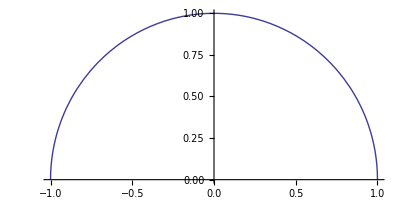

```mathematica
Integrate[2 √(1-x^2),{x,-1,1}] (*Multiplied by two because this only gave me the top half of my circle as shown in the plot*)
Plot[√(1-x^2),{x,-1,1},AspectRatio->1/2]
```

#### (#8) The volume of a sphere

Compute ∫_0^R ∫_0^π ∫_0^(2π) r^2 sin(θ)ⅆϕⅆθⅆr to obtain the well-known expression for the volume of a sphere.

```mathematica
Integrate[r^2 Sin[θ],{ϕ,0,2π},{θ,0,π},{r,0,R}]
```

(4 π R^3)/3

#### (#9) The surface area of a torus

(a) A torus is defined by two radii: the radius R of the θ circle that runs through the center of the tube, and the smaller cross-sectional radius r of the ϕ circle.  The parametric function that describes this surfaces is copied here from Lab 3.  Evaluate the cell below to plot a torus with R = 1 and r = 1/2.

```mathematica
torus= {Cos[phi](R+r Sin[theta]), Sin[phi](R+r Sin[theta]), r Cos[theta]};
ParametricPlot3D[torus/.{R->1,r->1/2},{phi,0,2 Pi},{theta,0,2 Pi}]
```

-Graphics3D-

(b) Determine the surface area of a torus, where radii R and r are treated as unspecified variables.  Hint: the differential area of a torus is (R+r sin(θ))rⅆϕⅆθ, where θ and ϕ both run from 0 to 2π.

```mathematica
Integrate[(R+r*Sin[θ])*r,{ϕ,0,2π},{θ,0,2π}]
```

4 π^2 r R

(c) Use variable replacement to evaluate the surface area of the torus when {R → 1, r → 1/2}.

```mathematica
Integrate[(R+r*Sin[θ])*r,{ϕ,0,2π},{θ,0,2π}]/.{r->1.2,R->1}
```

47.3741

#### (#10) The length of an arc

Plot the parabolic arc defined by the equation y = 1-x^2 over the range {x, -1, 1}.  Determine the numeric length of this arc as a floating-point number.
Hints: the length of a curve in the xy plane can be computed as ∫√(1+(dy/dx)^2)ⅆx.  Calculate the derivative in terms of x, substitute it into the integrand, and integrate over the appropriate range.

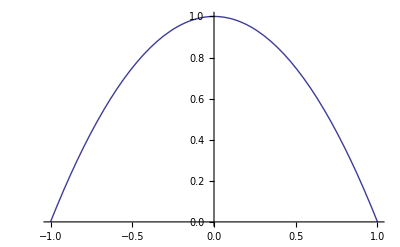

2.95789

```mathematica
y10 = 1-x^2;
Plot[y10,{x,-1,1}]
dy10 = D[y10,x];
Integrate[√(1+(dy10)^2),{x,-1,1}]//N
```

### (#11) Gauss's law surface integral (10 min)

The vector electric field at position r = {x, y, z} associated with a point charge Q at the origin is E=Q/(4π ϵ_0) r/r^3.  From Gauss' Law, we know that the total electric flux exiting a closed surface containing the charge is  Φ=∫E·ⅆA = Q/ϵ_0.  Your task here is to demonstrate this is true by computing ∫E·ⅆA over the cube that spans the range from -1 to +1 along all three axes.

Hints:  Since we know by symmetry that one sixth of the total flux will exit a specific face of the cube, you can compute the integral across the z = +1 face and multiply the result by 6.  Because ⅆA = ⅆx ⅆy ẑ on this face, E·ⅆA = E_z ⅆx ⅆy = Q/(4π ϵ_0) z/((x^2+y^2+1)^(3/2)) ⅆx ⅆy.

```mathematica
Clear["Global`*"]
6*Integrate[Q/(4*π*Subscript[ϵ, 0])*1/((x^2+y^2+1)^(3/2)),{x,-1,1},{y,-1,1}]
```

Q/ϵ_0

### (#12) The period of a simple pendulum (15 min)

In the previous lab, you learned that a simple pendulum is not all that simple.  Rather than being a nice harmonic oscillator with an amplitude-independent frequency of ω_0=√(g/L), it is significantly anharmonic and has a strongly amplitude-dependent frequency.  If the ideal harmonic-pendulum period is τ_0 = (2π)/ω_0 =2π √(L/g), then the actual period is τ = 4 τ_0 K(sin(θ_0/2)), where K represents a complete elliptic integral of the first kind.  Your job now is to use Mathematica to derive this relationship.  Recall that the traditional K(m) is equivalent to Mathematica's EllipticK(m^2).

(a) The total energy of the system is 1/2 m v^2 + m g h, where h = - L cos(θ).  By energy conservation, we know that the total energy is equal to the potential energy at the top of the swing (i.e. at θ = θ_0) where the velocity v is zero.  Thus we can write the energy as  1/2 m v^2-m g L cos(θ) = -m g L cos(θ_0).  Starting with this equation, solve for the velocity, which will now be expressed in terms of g, L,  θ and θ_0, and name the result velocity.  Tips: Rather than using special symbols for your angles, try boring names like th and th0.  While it shouldn't matter, we find that students have less trouble if they do this.

```mathematica
Clear[v]
hi =Solve[1/2 m*v^2-m*g*L*Cos[th]==-m*g*L*Cos[th0],v][[2]]
vel= v/.hi
```

{v→√2 √(g L cos(th)-g L cos(th0))}

√2 √(g L cos(th)-g L cos(th0))

(b) Because the pendulum swings on a circular arc, v = (d(L θ))/dt= L dθ/dt, which we can rearrange as dt = L/v dθ.  Now, using your expression for velocity, compute the period of the pendulum: τ(θ_0)= 4∫_0^θ_0 L/(v(θ))ⅆθ and name the result firsttry.  The factor of 4 accounts for the fact that a swing from 0 to θ_0 only represents one fourth of a period.  The integral will take a while to compute -- be patient.

```mathematica
firsttry =4*Integrate[L/vel,{th,0,th0}]
```

(4 √2 L √(-cot(th0/2)) th0/2csc^2(th0/2))/(√(-g L sin(th0)))

(c) If you got a messy result that includes an incomplete elliptical integral (EllipticF), then life is not good.  Because Mathematica was apparently worried about the values of some of your constants (especially θ_0),   Simplify firsttry based on the following important assumptions: {0 < th0 < π, g > 0, L > 0}.  Because that still won't get rid of the EllipticF, further FunctionExpand the simplified result, while again assuming that {0 < th0 < π}.  This should yield the more friendly EllipticK function.  Get help if this takes more than a few minutes.

```mathematica
Simplify[firsttry,{0<th0<π,g>0,L>0}]
```

4 √(L/g) csc(th0/2) th0/2csc^2(th0/2)

(d)  A more convenient way to get straight to the nicer expression is to incorporate Assumptions → {0 < th0 < π, g > 0, L > 0} as an option within Integrate.  Try this in the cell below, and assign a name to the result.

```mathematica
secondtry = 4*Integrate[L/vel,{th,0,th0},Assumptions->{0<th0<π,g>0,L>0}]
```

(4 L sin^2(th0/2))/(√(g L))

(e)  Use variable replacement to evaluate the period of the pendulum when {L → 1, g → 1}, and plot the result over the range {th0, 0, π} with PlotRange → {0, 50}.  Use some physical intuition to explain the divergence in the graph to your TA.

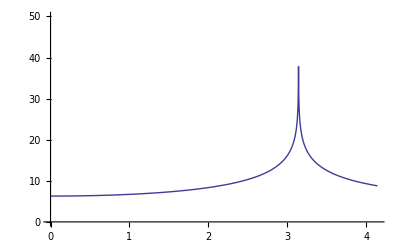

```mathematica
Plot[secondtry/.{L->1,g->1},{th0,0,π+1},PlotRange->{0,50},GridLines->{{π},{}}]
secondtry/.{L->1,g->1,th0->π}
```

### (#13) Monte Carlo Integration (20 min)

The most important feature of a numerical integration method is its choice of sample points.  Unlike an analytical integral, which effectively operates in the limit of an infinite number of samples, a numerical integral only takes a finite number of samples.  The key to any numerical-integration strategy is its algorithm for selecting the sample points. 

 "Monte Carlo" integration, one of the most important and widely-used techniques, is based on random sampling throughout the integration region.  Using the Monte Carlo approach, a one-dimensional integral is computed as ∫_a^b f(x)ⅆx = (b-a)/n∑_i^n f(x_i), where the sum runs over n evaluations of f at random values of x_i.  The larger the number of random samples, the more accurate the integration.  

(a) Evaluate the cells below (modified from the Neat Examples section of the NIntegrate reference page) to reveal the points sampled while integrating the volume of an unusual 3D shape.  Compare the sample points selected by the TrapezoidalRule algorithm to those selected by the MonteCarlo algorithm.  This should help you to better appreciate the brute-force nature of a random-sampling techniques.

```mathematica
region = (y-1)^2+z^2<1 &&(x-1)^2+z^2<1;
RegionPlot3D[region,{x,0,2},{y,0,2},{z,0,1},BoxRatios->Automatic,Mesh->False,PlotPoints->50, AxesLabel->{"x","y","z"}]
```

-Graphics3D-

```mathematica
Reap[NIntegrate[Boole[region],{z,0,1},{y,0,2},{x,0,2},
Method->"TrapezoidalRule",PrecisionGoal->4,EvaluationMonitor:>  Sow[{x,y,z}]]][[2,1]] // Point // Graphics3D
```

-Graphics3D-

Look up Sow and Reap in the DC and explain to your TA how the above statement works.

```mathematica
ans=Reap[NIntegrate[Boole[region],{z,0,1},{y,0,2},{x,0,2},
Method->"MonteCarlo",PrecisionGoal->2.5,MaxPoints->100000,EvaluationMonitor:>If[region,Sow[{x,y,z}]]]];
ans[[1]] (* result, extact is 2-2/3 *)
ans[[2,1]] // Point // Graphics3D (* graph of points used *)
```

2.67028

-Graphics3D-

(b) Create function circ[x_] := Sqrt[1-x^2] and plot it over the range {x, -1, 1} with AspectRatio → Automatic and Filling → Axis.  Integrate the function over the same range.

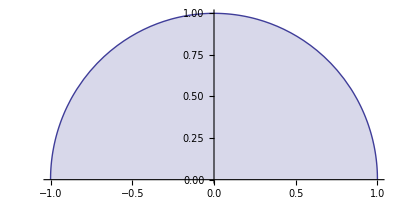

π/2

```mathematica
circ[x_]:=√(1-x^2)
Plot[circ[x],{x,-1,1},AspectRatio->Automatic,Filling->Axis]
Integrate[circ[x],{x,-1,1}]
```

(c) In order to estimate the area under the curve above, create a function, mc[n_], that performs an n-sample Monte Carlo integral of circ(x) over the range {x, -1, 1}.  See the summation formula in the description above.  You may not use NIntegrate for this problem.

```mathematica
mc[n_]:=(1+1)/n*circ/@RandomReal[{-1,1},n]//Total
```

(d) Use mc to perform a 10-sample estimate of the area and subtract the exact result (π/2), displaying the error to 10 decimal places.  Repeat for n = 10^2, 10^3, 10^4, 10^5 and 10^6.

```mathematica
N[mc[10]-π/2,10]
N[mc[10^2]-π/2,10]
N[mc[10^3]-π/2,10]
N[mc[10^4]-π/2,10]
N[mc[10^5]-π/2,10]
N[mc[10^6]-π/2,10]
```

-0.0196264

0.0519512

0.00495376

0.00793341

0.00233088

-0.000342774

### Orthogonal functions (optional, 15 min)

Every vector space has a basis, or in other words, a set of independent vectors that span the space.  Given a set of basis vectors {b_1, b_2, . . .b_n} that span an n-dimensional vector space, any vector in the space can be written as a unique linear combination of the basis vectors:  v=c_1 b_1+c_2 b_2+ . . . +c_n b_n.  Of course, this basis isn't unique since you can always find other distinct but equivalent bases.  And some bases are more useful than others.  Orthogonal bases, where each pair of basis vectors is mutually orthogonal, are especially important.  In ordinary 3-dimensional space, the concept of "orthogonal" means "perpendicular".  Our favorite basis in 3D is the set of x̂, ŷ and ẑ unit vectors that point along the x, y and z axes, respectively.  We like this basis precisely because these basis vectors are orthogonal.

Many applications (e.g. quantum mechanics, electrostatics, optics, etc.) require that we generalize the concept of vector space to include continuous functions of one or more variables.  Just as we can decompose a 3D vector over an orthogonal basis of unit vectors (i.e. break it up into its x, y and z components), we can decompose a function like 1-x^2 over a set of orthogonal basis functions.  A few common examples include sine and cosine harmonics (Fourier analysis), spherical harmonics, Legendre polynomials, Hermite polynomials and Bessel functions.

(a) We'll walk you through the first example.  We say that the functions sin(m x) and cos(n x) are that orthogonal if 1/π∫_0^(2π) sin(m x)cos(n x)ⅆx = 0, where m and n are both integers.  This is the function-space equivalent of a dot product test.  Evaluate the cell below to see that sin(m x) and cos(n x) are always orthogonal, regardless of the integer values of m and n.  While it isn't hard conduct a more rigorous theortical analysis, a simple table (m and n both run from 1 to 5) of integral products illustrates the pattern of orthogonality quickly and intuitively.

```mathematica
intprod[m_,n_] :=  Integrate[Sin[m x]Cos[n x],{x,0,2Pi}]/Pi
intprod[m,n]
Table[intprod[m,n],{m,1,5},{n,1,5}]//MatrixForm
```

Here is another, more powerful way.

```mathematica
Simplify[Integrate[Sin[m x] Cos[n x],{x,0,2 Pi}]/Pi, Assumptions->{Element[m, Integers], Element[n, Integers]}]
```

(b) We can similarly define other orthgonality relations.  Copy and modify the code above to show that cos(m x) and cos(n x) are orthogonal only when n ≠ m.  Then repeat the exercise for sin(m x) and sin(n x).

(c) The Legendre polynomials L_m(x) and the associated Legendre polynomials L_m^n(x) are commonly encountered in quantum mechanics when dealing with atomic wave functions.  Generate a list of the first six (i.e. m runs from 0 to 5) Legendre polynomials (see LegendreP), and then plot them on the same graph over the range {x, -1, 1}.

(d) Legendre polynomials L_m(x) and L_n(x) are said to be orthogonal when (m+n+1)/2∫_-1^1 L_m(x)L_n(x)ⅆx = 0.  Create a table of integral products (let m and n run from 0 to 5) to illustrate that L_m(x) and L_n(x) are orthogonal only when m ≠ n.

## On Your Own (40 min)

### (#14) 1D kinematics (10 min)

From the previous lab, we found that the time-dependence of the acceleration of a vertically-fired projectile (mass m) under the influence of gravity (g) and air resistance (b) is a(t) = -(g +(b v_0)/m)ⅇ^(-(b t)/m), where x_0 and v_0 are the initial position and velocity, respectively.

(a)  Compute v(t)=v_0+∫_0^t a(t)ⅆt to obtain the time-dependence of the velocity.  Then compute y(t)=y_0+∫_0^t v(t)ⅆt to obtain the time-dependence of the position.

```mathematica
v[t_]:=v0 + Integrate[-(g+(b*v0)/m)Exp[-b*t/m],t]
y[t_]:= y0 +Integrate[v[t],t]
```

(b) Use variable replacement to determine the time-dependencies of the position, velocity and acceleration of the projectile when {y0 → 0, v0 → 100, g → 9.81, m → 1, b → 0.3}, and plot each of them separately.  You might want to refer to your previous lab for ideas.

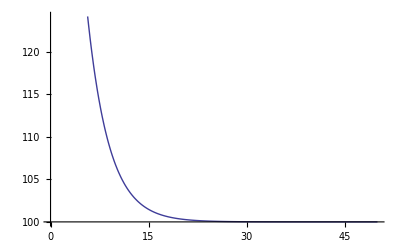

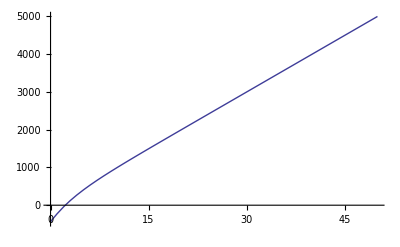

```mathematica
vplot =v[t]/.{y0->0,v0->100,g->9.81,m->1,b->0.3};
yplot = y[t]/.{y0->0,v0->100,g->9.81,m->1,b->0.3};
Plot[vplot,{t,0,50}]
Plot[yplot,{t,0,50}]
```

### (#15) 2D electric potential from a spherical charge distribution (15 min)

Consider a uniformly-charged hollow spherical shell of radius r and total charge Q.  Each bit of charge on the shell makes a small contribution dV to the electric potential at some point P a distance R from the center of the sphere.  So the total potential at P is V(R) = ∫(k dQ)/s where k is Coulomb's constant and s is the distance of the differential charge dQ from point P.  Our job now is to compute this two-dimensional integral over the surface of the shell.  First of all, dQ =σ dA, where σ = Q/(4π r^2) is the surface-charge density and dA = r^2 sin(θ) dθ dϕ is the differential area of dQ in spherical coordinates.  Thus, dQ = (Q sin(θ))/(4π) dθ dϕ.  Secondly, s is the length is the vector s that extends from point (r, θ, ϕ) on the surface of the sphere to point P a distance R along the z axis, and can be computed as s = √(s·s)=√((R-r cos(θ))^2+r^2 sin^2(θ)).  The total potential at point P is then ∫_0^(2π) ∫_0^π (kQ sin(θ))/(4π √((R-r cos(θ))^2+r^2 sin^2(θ)))ⅆθⅆϕ.

(a) Compute this integral to obtain the total electric potential at point P.   The integral may take quite a while to compute analytically -- be patient.

```mathematica
Integrate[(k*Q*Sin[θ])/(4π √((R- r*Cos[θ])^2+(r*Sin[θ])^2)),{θ,0,π},{ϕ,0,2π}]
```

ConditionalExpression[(2 k Q)/(√((r-R)^2)+√((r+R)^2)),(r/R+R/r∉ℝ∨Re(r/R+R/r)≥2∨Re(r/R+R/r)≤-2)∧r≠R∧r+R≠0]

(b) The output may be a mess since Mathematica needs to know more about the values of r and R in order to compute a useful result.  In the cell below, redo the integral while employing Assumptions →  {R > 0, r > 0, r ≠ R} as an option within Integrate.  Give this new result a name (e.g. niceresult).

```mathematica
nicerstuff = Integrate[(k*Q*Sin[θ])/(4π √((R- r*Cos[θ])^2+(r*Sin[θ])^2)),{θ,0,π},{ϕ,0,2π},Assumptions-> {R>0,r>0,r≠R}]
```

(k Q (-Abs[r-R]+r+R))/(2 r R)

(c) Now use variable replacement to evaluate your potential for the simple case where {k → 1, Q → 1, r → 1}.  Plot the resulting expression (which should depend only on R) over the range {R, 0, 5} using PlotRange→{0, 1.1}.  Try to explain this rather surprising result to your TA?

(-Abs[1-R]+R+1)/(2 R)

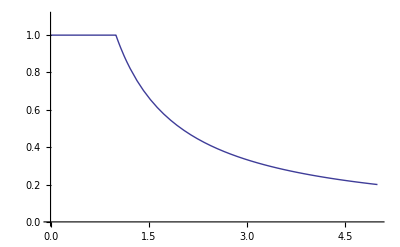

```mathematica
plotstuff = nicerstuff/.{k->1,Q->1,r->1}
Plot[plotstuff,{R,0,5},PlotRange->{0,1.1}] (*shows that the electric potential doesn't start to fall off until you get outisde the sphere *)
```

Does this look physically reasonable?  (Explain to your TA why or why not.)

### (#16) Variational Principle (15 min)

A useful technique in quantum mechanics (and other areas of physics) is called the variational principle.  In quantum mechnics, it can be used to find the approximate energy of a particle and its wave function even when this can’t be done exactly.  The wave function is the square root of the probability of finding a particle in a particular region of space.  The way the variational principle works is that you guess a wave function which has a functional form you think might be about right but which has one or more adjustable parameters.  Then you compute a value for the approximate energy of the system as a function of these parameters.  The principle states that the parameter which gives the lowest energy is the one which best approximates the wave function.  The associated energy is the best approximation of the energy as well.

Let’s start by defining a constant η we’ll need in our calculation.  We are going to compute the energy in units called electron Volts (eV) and distances in nanometers (1 nm = 10^-9 m).  We’ll need ℏ (Planck’s constant), c (the speed of light), m (the mass of an electron in our case), and then η which is a combination of these units.

```mathematica
ℏ=6.58212 10^-16;
c=2.998 10^18;
m=0.511 10^8;
η=(ℏ c )^2/(2m)
```

0.0381017

The units of η are nm^2.

Now, let’s construct a simple potential for which the energy cannot be computed analytically.  It is 3 eV for Abs[x]>0.25 and 0 for Abs[x]<0.25.

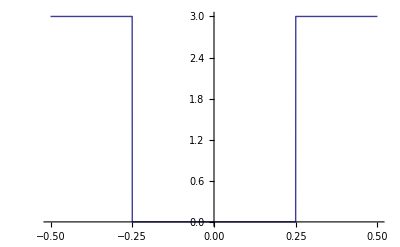

```mathematica
V[x_]:=3(1-UnitBox[2* x])
Plot[V[x],{x,-0.5,0.5}]
```

A reasonable guess for the wave function is a gaussian packet (just like the normal distribution we saw earlier).  ψ(x)=exp(-1/2 (x/σ)^2).  Plot this function over the range -0.3≤x≤0.3 for σ=0.1.

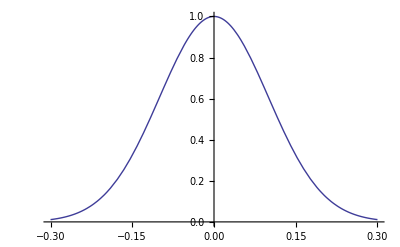

```mathematica
ψ[x_,σ_] := Exp[-1/2*((x/σ)^2)]
Plot[ψ[x,0.1],{x,-.3,.3}]
```

In order to user the variational principle in the form I prefer, it is important that the wave function be normalized.  In other words that ∫_(-∞)^∞ ψ(x)ⅆx==1.  Create a function phi[x,sigma] which is equal to a constant times ψ[x,σ] and is normalized in this way.  Check and make sure it satisifes the normalization condition.

```mathematica
const = constant/.Solve[Integrate[constant*ψ[x,0.1],{x,-∞,∞}]==1,constant][[1]]
Integrate[const * ψ[x,0.1],{x,-∞,∞}]
ϕ[x_,σ_]:=  const*ψ[x,σ]
```

3.98942

1.

The energy e(σ) for this state is ∫_(-∞)^∞ ϕ(x,σ) (V(x) ϕ(x,σ)-ηϕ''(x,σ))ⅆx.  Plot e[sigma] as a function of sigma and from this graph estimate the minimum energy and the value of σ for which this occurs.

```mathematica
e[σ_]:= Integrate[ϕ[x,σ]*(V[x]ϕ[x,σ]- η*D[ϕ[x,σ],{x,2}]),x]
Plot[e[σ],{σ,-.249,.249}]
```

$Aborted

#### Optional

Using FindRoot and the derivative of es, find the minimum energy and the value of σ which this occurs exactly.  Plot the potential V[x] and the wave function ϕ  on the same plot.

Usually the variational principle only works for finding the lowest energy of the system and its associated wave function.  In this case, we can actually find a good approximation of the next higher energy and state in the system as well.  This is because the symmetry of the system requires that the wave function be either symmtric (ψ(x)=ψ(-x)) or anti-symmetric ψ(x)==-ψ(-x).  In this case, the lowest state is symmetric and the next higher state is anti-symmtric.  So if we use an anti-symmtric guess for our wave function we’ll get the next higher state.  Try changing the above analysis using the anti-symmtric wave function ψ(x,σ)=x exp(-1/2 (x/σ)^2) and see what energy and state you get.  (Don’t forget to normalize the wave function.)  Plot the resulting wave function on the save graph is the potential V[x].